```mathematica
<<MaTeX`
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/mcmcclur/Documents/html/classes/Spring2020CalcIII/online_presentations/04.09.TripleIntegrals/images

```mathematica
Graphics3D[{
{Opacity[0.9],Cuboid[{-2,-1,0},{2,1,1}]},
Black,
Arrow[Tube[{{0,0,0},{3,0,0}}]],
Arrow[Tube[{{0,0,0},{0,3,0}}]],
Arrow[Tube[{{0,0,0},{0,0,2.5}}]],
Text[MaTeX["x",FontSize->18],{3.1,0,0}],
Text[MaTeX["y",FontSize->18],{0,3.1,0}],
Text[MaTeX["z",FontSize->18],{0,0,2.6}]
},PlotRange->{{-3,3},{-3,3},{0,3}},
ViewPoint->{1.25,1,0.65},Boxed->False,
ImageSize->800]
```

-Graphics3D-

```mathematica
f[x_,y_,z_] = (16-(x^2+y^2))(z+1);
dd = 0.05;
p = Image3D[
Table[Round[f[x,y,z]/32,0.02],{z,dd,1-dd,dd},{y,-1+dd,1-dd,dd},{x,-2+dd,2-dd,dd}],
ColorFunction->"StarryNightColors"];
{l,m,n} = ImageDimensions[p];
Show[{p,
Graphics3D[{
Black,
Arrow[Tube[{{l-1,m-1,0}/2,{l-1,m-1,5n}/2}]],
Arrow[Tube[{{l-1,m-1,0}/2,{2.9l-1,m-1,0}/2}]],
Arrow[Tube[{{l-1,m-1,0}/2,{l-1,4m-1,0}/2}]],
Thickness[0.00125],Line[{
{{0,0,n},{l,0,n},{l,m,n},{0,m,n},{0,0,n}},
{{0,0,0},{l,0,0},{l,m,0},{0,m,0},{0,0,0}},
{{0,0,0},{0,0,n}},{{l,m,0},{l,m,n}},
{{0,m,0},{0,m,n}},{{l,0,0},{l,0,n}}
}],
Text[MaTeX["z",FontSize->18],1.06{l-1,m-1,5n}/2],
Text[MaTeX["x",FontSize->18],1.02{2.9l-1,m-1,0}/2],
Text[MaTeX["y",FontSize->18],1.04{l-4,4m-1,0}/2]
}]
}, Boxed->False, ImageSize -> 700,ViewPoint->{1.25,1,0.65}]
```

-Graphics3D-

```mathematica
Graphics3D[{{Opacity[0.7],
{Black,Polygon[DiagonalMatrix[{a,b,0}]]},
Polygon[DiagonalMatrix/@{{a,0,c},{0,b,c},{a,b,c}}]},
{Black,
Arrow[Tube[{{0,0,0},{a+r,0,0}}]],
Arrow[Tube[{{0,0,0},{0,b+r,0}}]],
Arrow[Tube[{{0,0,0},{0,0,c+r}}]]},
Text[MaTeX["x",FontSize->18],{a+r+s,0,0}],
Text[MaTeX["y",FontSize->18],{0,b+r+s,0}],
Text[MaTeX["z",FontSize->18],{0,0,c+r+s}],
Text[MaTeX[a,FontSize->18],{a,s,0}],
Text[MaTeX[b,FontSize->18],{1.2s,b,0}],
Text[MaTeX[c,FontSize->18],{-s,0,c}],
Text[MaTeX["z=1-x/3-y/2",FontSize->18],{1.6,1,1.8}],
Arrow[{{1.6,1,1.7},{1,0.5,L[1,0.5]}}]
}, Boxed->False,ImageSize->500, ViewPoint -> {1.34,-2.69,1.55}/2]
```

-Graphics3D-

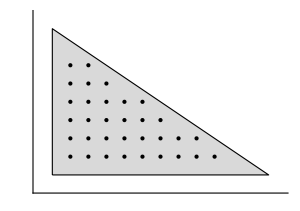
-Graphics- | -Graphics-

```mathematica
{a,b,c} = {3,2,1};
r = 1; s = 0.1;d=0.25;
L[x_,y_] = 1-x/3-y/2;
arrows3D =Image[ImageTake[ Rasterize[Graphics3D[{{Opacity[0.7],
{Black,Polygon[DiagonalMatrix[{a,b,0}]]},
Polygon[DiagonalMatrix/@{{a,0,c},{0,b,c},{a,b,c}}]},
{Black,
Arrow[Tube[{{0,0,0},{a+r,0,0}}]],
Arrow[Tube[{{0,0,0},{0,b+r,0}}]],
Arrow[Tube[{{0,0,0},{0,0,c+r}}]]},
{Black,Arrowheads[0.02],Table[
Arrow[Tube[{{x,y,0},{x,y,L[x,y]}}]],
{y,d,2-d,d},{x,d,3-3 y/2-d,d}]},
Text[MaTeX["x",FontSize->18],{a+r+s,0,0}],
Text[MaTeX["y",FontSize->18],{0,b+r+s,0}],
Text[MaTeX["z",FontSize->18],{0,0,c+r+s}],
Text[MaTeX[a,FontSize->18],{a,s,0}],
Text[MaTeX[b,FontSize->18],{1.2s,b,0}],
Text[MaTeX[c,FontSize->18],{-s,0,c}],
Text[MaTeX["z=1-x/3-y/2",FontSize->18],{1.6,1,1.8}],
Arrow[{{1.6,1,1.8},{1,0.5,L[1,0.5]}}]
}, Boxed->False,ImageSize->500, ViewPoint -> {1.34,-2.69,1.55}/2],
ImageResolution->1500, ImageSize->500],{50,500},{0,400}], ImageSize -> 350,ImageResolution->2100];
triangle = Graphics[{{EdgeForm[Black],LightGray,
Polygon[{{0,0},{3,0},{0,2}}]},
Point[Flatten[Table[
{x,y},
{y,d,2-d,d},{x,d,3-3 y/2-d,d}],1]]
}, Axes -> True,ImageSize->300,
PlotRange->{{-0.2,3.2},{-0.2,2.2}},
Ticks-> {{{3,MaTeX[3, FontSize->16]}},{{2,MaTeX[2,FontSize->16]}}}];
Grid[{{arrows3D,triangle}}]
```

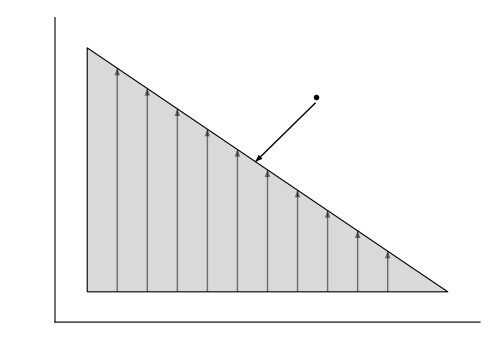

```mathematica
Graphics[{{EdgeForm[Black],LightGray,
Polygon[{{0,0},{3,0},{0,2}}]},
{Opacity[0.5],
Table[Arrow[{{x,0},{x,2-2x/3}}],{x,0.25,2.5,0.25}]},
Text[MaTeX["y=2-2x/3", FontSize->16],{1.9,1.6}],
Arrow[{{1.9,1.55},{1.4,2-2*1.4/3}}]
}, Axes -> True,ImageSize->500,
PlotRange->{{-0.2,3.2},{-0.2,2.2}},
Ticks-> {{{3,MaTeX[3, FontSize->16]}},{{2,MaTeX[2,FontSize->16]}}}]
```

```mathematica
Export["triangular_integration.png",%]
```

triangular_integration.png